```mathematica
(* Logistic Equation *)
ode = {D[P[t],t] - r*P[t] + r*P[t]^2/k == 0, P[0]==p0};
sol1 = DSolve[ode, P, t]
(* AGREES WITH https://math.libretexts.org/Bookshelves/Calculus/Calculus_(OpenStax)/08%3A_Introduction_to_Differential_Equations/8.04%3A_The_Logistic_Equation*)
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{P→Function[{t},(ⅇ^(r t) k p0)/(k-p0+ⅇ^(r t) p0)]}}

```mathematica
Simplify[ode /. sol1]
```

{{True,True}}

```mathematica
(* Obtain function from the solution *)
p[t_] = P[t] /. First @ sol1
p[t]+a*D[p[t],t]+a^2*D[p[t],t,t]/2 + a^3*D[p[t],t,t,t]/6;
Simplify[%, 6+6a*r+3a^2r^2+a^3r^3 == ⅇ^(a*r)];

(* Example of finite symmetry from Lie algebra *)
Print["P[t+5]: ", Simplify[D[p[t+5],t] - r*p[t+5] + r*(p[t+5])^2 / k == 0]]
(* Example of finite transformation not in Lie algebra *)
Print["P[t+1], P[t+2]: ", Simplify[D[p[t+1],t] - r*p[t+2] + r*(p[t+2])^2 / k == 0]]
(* Another example of finite transformation not in Lie algebra *)
Print["P[3t]: ", Simplify[D[p[t/3],t] - r*p[t/3] + r*(p[t/3])^2 / k == 0]]

(* Testing Transformation that is always true (PDE in (t') of P(t'))*)
Simplify[3*D[p[t/3],t] - r*p[t/3] + r*p[t/3]^2/k == 0]
(* Testing nonvalid symmetry transformation that is in old(PDE in (t) of P(t'))*)
Simplify[D[p[t/3],t] - r*p[t/3] + r*p[t/3]^2/k == 0]
```

(ⅇ^(r t) k p0)/(k-p0+ⅇ^(r t) p0)

P[t+5]: True

P[t+1], P[t+2]: ((ⅇ^(r (1+t))-ⅇ^(r (2+t))) k (k-p0) p0 (k^2-2 k p0-(-1+ⅇ^(r (3+2 t))) p0^2) r)/((k+(-1+ⅇ^(r (1+t))) p0) (k+(-1+ⅇ^(r (2+t))) p0))==0

P[3t]: (ⅇ^((r t)/3) k (k-p0) p0 r)/(k+(-1+ⅇ^((r t)/3)) p0)==0

True

(ⅇ^((r t)/3) k (k-p0) p0 r)/(k+(-1+ⅇ^((r t)/3)) p0)==0

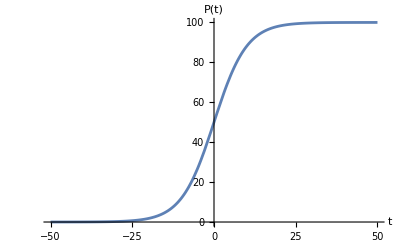

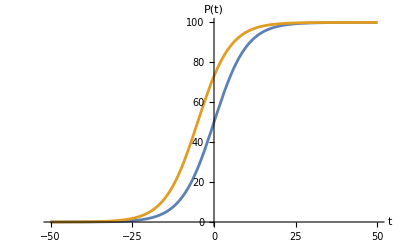

```mathematica
Plot[{p[t]} /. {p0 -> 50, k->100,r->0.2}, {t, -50, 50}, AxesLabel->{t,P[t]}, LabelStyle->{Bold, Black}]
Plot[{{p[t] } /. {p0 -> 50, k->100,r->0.2}, p[t+5] /. {p0 -> 50, k->100,r->0.2}}, {t, -50, 50}, AxesLabel->{t,P[t]}, LabelStyle->{Bold, Black}]
```

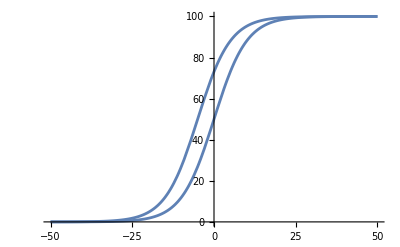

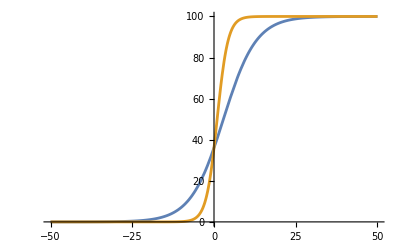

```mathematica
Plot[{p[t], p[t+5]} /. {p0 -> 50, k->100,r->0.2}, {t, -50, 50}]
Plot[{{p[t] } /. {p0 -> 36, k->100,r->0.2}, p[3*t] /. {p0 -> 36, k->100,r->0.2}}, {t, -50, 50}]
```

```mathematica
(* (1+1)d HEAT EQUATION *)
Clear[u]
heatOde = {D[u[x,t],t] - D[u[x,t],x,x] == 0}
heatSol = DSolve[heatOde, u, {x,t}]

Simplify[heatOde /. heatSol]

u[x_, t_] = u[x,t] /. First @ heatSol
```

{u^(0,1)[x,t]-u^(2,0)[x,t]==0}

DSolve::lpde: General solution is not available for the given linear partial differential equation. Trying to build a special solution.

{{u→Function[{x,t},1+Cosh[C[1]+x C[2]+t C[2]^2]+Sinh[C[1]+x C[2]+t C[2]^2]]}}

{{True}}

1+Cosh[C[1]+x C[2]+t C[2]^2]+Sinh[C[1]+x C[2]+t C[2]^2]

```mathematica
(* Simple Symmetry Example (Spatial translation)*)
D[u[x,t],t] - D[u[x,t],x,x] == 0
D[u[x+4,t+2],t] - D[u[x+4,t+2],x,x] == 0
```

True

True

```mathematica
(* Plotting the original and transformed solutions *)
Print["Regular u[x,t] Plot"]
Plot3D[{u[x,t] /. {C[1] -> 1, C[2] -> 1}}, {x, -5, 5}, {t, 0, 5}]
Animate[Plot[{u[x,t] /. {C[1] -> 1, C[2] -> 1}}, {x, -5, 5}], {t, 0, 10}, AnimationRunning->False]

Print["u[x+2,t+3] Plot"]
Plot3D[u[x+2,t+3] /. {{C[1] -> .1, C[2] -> .1}}, {x, -5, 5}, {t, 0, 5}]
```

Regular u[x,t] Plot

-Graphics3D-

u[x+2,t+3] Plot

-Graphics3D-

```mathematica
(* Different Symmetry Example (Time and spatial change)*)
D[u[x*Exp[2],t*Exp[4]],t] - D[u[x*Exp[2],t*Exp[4]],x,x] == 0   (* Epsilon = 4*)
D[u[x*Exp[3],t*Exp[4]],t] - D[u[x*Exp[3],t*Exp[4]],x,x] == 0   (* Epsilon is different for x (eps=3) and t (eps=4)*)
```

True

ⅇ^4 C[2]^2 Cosh[C[1]+ⅇ^3 x C[2]+ⅇ^4 t C[2]^2]-ⅇ^6 C[2]^2 Cosh[C[1]+ⅇ^3 x C[2]+ⅇ^4 t C[2]^2]+ⅇ^4 C[2]^2 Sinh[C[1]+ⅇ^3 x C[2]+ⅇ^4 t C[2]^2]-ⅇ^6 C[2]^2 Sinh[C[1]+ⅇ^3 x C[2]+ⅇ^4 t C[2]^2]==0

```mathematica
(* Another symmetry example (Galilean Boost) *)
Clear[eps]
utrnew[x_,t_] = Exp[-ϵ*x+ϵ^2*t]*f[x,t];
D[utrnew[x,t],t] - D[utrnew[x,t],x,x] == 0;
Simplify[%];
Simplify[%, Derivative[1,0][f[x,t]]-Derivative[0,2][f[x,t]]==0]; (* *)

D[c*Exp[-ϵ*x+ϵ^2*t],t] - D[c*Exp[-ϵ*x+ϵ^2*t],x,x] == 0; (* Simplest transformed solution fits original PDE *)
D[Exp[-ϵ*x+ϵ^2*t]*(x-2*ϵ*t),t] - D[Exp[-ϵ*x+ϵ^2*t]*(x-2*ϵ*t),x,x] == 0; (* u(x,t)=x also fits original PDE *)

D[Exp[-ϵ*x+ϵ^2*t]*u[x-2*ϵ*t,t], t] - D[Exp[-ϵ*x+ϵ^2*t]*u[x-2*ϵ*t,t],x,x] == 0; (* general solution given by MATHEMATICA does fit original PDE after simplify*)
Simplify[%];

eps = 2;
Print[Row[{TraditionalForm[HoldForm[u[x,t] = c*e^(-ϵ*x+(ϵ^2)*t)]]}]]
Plot3D[c*Exp[-eps*x+(eps^2)*t] /. {c -> 2}, {x, -5, 5}, {t, 0, 5}]
Animate[Plot[c*Exp[-eps*x+(eps^2)*t] /. {c -> 2}, {x, -5, 5}], {t, 0, 10}, AnimationRunning->False]
Animate[Plot3D[c*Exp[-ϵ*x+(ϵ^2)*t] /. {c -> 2}, {x, -5, 5}, {t, 0, 10}], {ϵ, 0, 1}, AnimationRunning->False]

Print[Row[{TraditionalForm[HoldForm[u'[x,t] = u[x-2ϵt,t]*e^(-ϵ*x+(ϵ^2)*t)]]}]]
Plot3D[Exp[-eps*x+(eps^2)*t]*u[x-2*eps*t,t] /. {{C[1] -> .1, C[2] -> .1}}, {x, -5, 5}, {t, 0, 5}]
Animate[Plot3D[Exp[-ϵ*x+(ϵ^2)*t]*u[x-2*ϵ*t,t] /. {{C[1] -> .1, C[2] -> .1}}, {x, -5, 5}, {t, 0, 10}], {ϵ, 0, 1}, AnimationRunning->False]
```

u(x,t)=c e^(-ϵ x+ϵ^2 t)

-Graphics3D-

u'(x,t)=u(x-2 ϵt,t) e^(-ϵ x+ϵ^2 t)

-Graphics3D-

```mathematica
(* Another symmetry example (non-finite transformation?) FROM: https://www.mdpi.com/2073-8994/12/3/359 *)
Clear[eps]
utrnew[x_,t_] = c*Exp[-ϵ*x^2/(1+4*ϵ*t)]/Sqrt[1+4*ϵ*t]*f[x/(1+4*ϵ*t),t/(1+4*ϵ*t)];
D[utrnew[x,t],t] - D[utrnew[x,t],x,x] == 0;
Simplify[%]

(* Transformed constant solution does fit PDE*)
D[c*Exp[-ϵ*x^2/(1+4*ϵ*t)]/Sqrt[1+4*ϵ*t],t] - D[c*Exp[-ϵ*x^2/(1+4*ϵ*t)]/Sqrt[1+4*ϵ*t],x,x] == 0;
D[(x/(1+4*ϵ*t))*Exp[-ϵ*x^2/(1+4*ϵ*t)]/Sqrt[1+4*ϵ*t],t] - D[(x/(1+4*ϵ*t))*Exp[-ϵ*x^2/(1+4*ϵ*t)]/Sqrt[1+4*ϵ*t],x,x] == 0;

(* Transformed MATHEMATICA solution fits original ODE after simplify*)
D[Exp[-ϵ*x^2/(1+4*ϵ*t)]/Sqrt[1+4*ϵ*t]*u[x/(1+4*ϵ*t),t/(1+4*ϵ*t)],t] - D[Exp[-ϵ*x^2/(1+4*ϵ*t)]/Sqrt[1+4*ϵ*t]*u[x/(1+4*ϵ*t),t/(1+4*ϵ*t)],x,x] == 0;
Simplify[%]

eps = 0.05;
Print[Row[{TraditionalForm[HoldForm[u[x,t] = c*Exp[-ϵ*x^2/(1+4*ϵ*t)]/(1+4ϵ*t)]]}]]
(* Plot3D[c*Exp[eps*x^2/(1-4*eps*t)]/(1-4*eps*t) /. {c -> 2}, {x, -5, 5}, {t, 0, 5}] *)
Animate[Plot[c*Exp[-eps*x^2/(1+4*eps*t)]/Sqrt[1+4*eps*t] /. {c -> 2}, {x, -5, 5}], {t, 0, 10}, AnimationRunning->False]
Animate[Plot3D[c*Exp[-ϵ*x^2/(1+4*ϵ*t)]/Sqrt[1+4ϵ*t] /. {c -> 2}, {x, -5, 5}, {t, 0, 10}], {ϵ, 0, 1}, AnimationRunning->False]

Print[Row[{TraditionalForm[HoldForm[u'[x,t] = c*Exp[ϵ*x^2/(1-4*ϵ*t)]/(1-4*ϵ*t)*f[x/(1-4*ϵ*t),t/(1-4*ϵ*t)]]]}]]
(* Plot3D[Exp[-eps*x^2/(1+4*eps*t)]/(1+4*eps*t)*u[x/(1+4*eps*t),t/(1+4*eps*t)] /. {{C[1] -> .1, C[2] -> .1}}, {x, -5, 5}, {t, 0, 5}] *)
Animate[Plot3D[Exp[-ϵ*x^2/(1+4*ϵ*t)]/Sqrt[1+4*ϵ*t]*u[x/(1+4*ϵ*t),t/(1+4*ϵ*t)] /. {{C[1] -> .1, C[2] -> .1}}, {x, -5, 5}, {t, 0, 10}], {ϵ, 0, 1}, AnimationRunning->False]
```

(c ⅇ^(-(x^2 ϵ)/(1+4 t ϵ)) (f^(0,1)[x/(1+4 t ϵ),t/(1+4 t ϵ)]-f^(2,0)[x/(1+4 t ϵ),t/(1+4 t ϵ)]))/(1+4 t ϵ)^(5/2)==0

True

u(x,t)=(c exp(-(ϵ x^2)/(1+4 ϵ t)))/(1+4 ϵ t)

u'(x,t)=(c exp((ϵ x^2)/(1-4 ϵ t)) f(x/(1-4 ϵ t),t/(1-4 ϵ t)))/(1-4 ϵ t)

```mathematica
(* TESTING WITH BOUNDARY CONDITIONS *)
Clear[u]
heatOde = {D[u[x,t],t] - D[u[x,t],x,x] == 0, {u[-5,t]==0, u[5,t]==0, u[x,0]==(-x^2+25)/50}}
heatSol = DSolve[heatOde, u, {x,t}] (* Solution found by Mathematica *)

u_test[x_,t_] = Sum[-400*(-1+(-1)^n)*Exp[-Pi^2*t*n^2/100]*Sin[Pi*n*(5+x)]/(Pi*n)^3, {n, 1, 10}]

D[Exp[-ϵ*x+ϵ^2*t]*u_test[x-2*ϵ*t,t],t] - D[Exp[-ϵ*x+ϵ^2*t]*u_test[x-2*ϵ*t,t],x,x] == 0
FullSimplify[%]

Animate[Plot[u_test[x,t], {x, -5, 5}], {t, 0, 5}, AnimationRunning->False]
Animate[Plot[Exp[-ϵ*x+ϵ^2*t]*u_test[x-2*ϵ*t,t] /. {ϵ -> 0.1}, {x, -5, 5}], {t, 0, 5}, AnimationRunning->False]
Animate[Plot3D[Exp[-ϵ*x+ϵ^2*t]*u_test[x-2*ϵ*t,t], {x, -5, 5}, {t, 0, 5}], {ϵ, 0, 1}, AnimationRunning->False]
```

{u^(0,1)[x,t]-u^(2,0)[x,t]==0,{u[-5,t]==0,u[5,t]==0,u[x,0]==1/50 (25-x^2)}}

{{u→Function[{x,t},-(8 (-1+(-1)^K[1]) ⅇ^(-1/100 π^2 t K[1]^2) Sin[1/10 π (5+x) K[1]])/(π^3 K[1]^3)K[1]1∞]}}

(800 ⅇ^(-(π^2 t)/100) Sin[π (5+x)])/π^3+(800 ⅇ^(-(9 π^2 t)/100) Sin[3 π (5+x)])/(27 π^3)+(32 ⅇ^(-(π^2 t)/4) Sin[5 π (5+x)])/(5 π^3)+(800 ⅇ^(-(49 π^2 t)/100) Sin[7 π (5+x)])/(343 π^3)+(800 ⅇ^(-(81 π^2 t)/100) Sin[9 π (5+x)])/(729 π^3)

2 ⅇ^(-x ϵ+t ϵ^2) ϵ u_test^(1,0)[x-2 t ϵ,t]+ⅇ^(-x ϵ+t ϵ^2) (u_test^(0,1)[x-2 t ϵ,t]-2 ϵ u_test^(1,0)[x-2 t ϵ,t])-ⅇ^(-x ϵ+t ϵ^2) u_test^(2,0)[x-2 t ϵ,t]==0

ⅇ^(ϵ (-x+t ϵ)) (u_test^(0,1)[x-2 t ϵ,t]-u_test^(2,0)[x-2 t ϵ,t])==0